```mathematica
ClearAll["Global`*"]
```

```mathematica
D1[z_] := Grid[Table[ Binomial[z+j-1,z-1] z^k/k!,{j,0,7},{k,0,7}]]
D1a[z2_] := Grid[Table[ Limit[Binomial[z+j-1,z-1] z^k/k!/z,z->z2],{j,0,7},{k,0,7}]]

K[n_,k_] := K[n,k]=Sum[ FullSimplify[MangoldtLambda[j]/Log[j]] K[Floor[n/j],k-1],{j,2,n}];K[n_,0]:=1

E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
EP2[n_,a_,b_] := EP2[n,a,b]=Sum[SeriesCoefficient[Series[(Log[x+1])^a,{x,0,230}],k]E2a[n,k,b],{k,1,Log[If[b>2,2,b],n]}];EP2[n_,0,b_]:=1
D1[n_, a_, b_] := Sum[ Binomial[a+j-1,a-1] b^j a^k/k! EP2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]
D1a[n_, a_, b_] := Grid[Table[ Binomial[a+j-1,a-1] b^j a^k/k! EP[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
D1b[n_, a2_, b_] := Grid[Table[ Limit[Binomial[a+j-1,a-1] b^j a^k/k! EP[n/b^j,k,b]/a,a->a2],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
D1c[n_, a_, b_] := Grid[Table[ Binomial[a+j-1,a-1] b^j a^k/k! EP2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]]
```

```mathematica
D1[-1]
```

1 | -1 | 1/2 | -1/6 | 1/24 | -1/120 | 1/720 | -1/5040
-1 | 1 | -1/2 | 1/6 | -1/24 | 1/120 | -1/720 | 1/5040
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
D1[1]
```

1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040
1 | 1 | 1/2 | 1/6 | 1/24 | 1/120 | 1/720 | 1/5040

```mathematica
D1a[0]
```

∞ | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
D1a[100,1,2]
```

EP[100,0,2] | EP[100,1,2] | 1/2 EP[100,2,2] | 1/6 EP[100,3,2] | 1/24 EP[100,4,2] | 1/120 EP[100,5,2] | 1/720 EP[100,6,2]
2 EP[50,0,2] | 2 EP[50,1,2] | EP[50,2,2] | 1/3 EP[50,3,2] | 1/12 EP[50,4,2] | 1/60 EP[50,5,2] | 
4 EP[25,0,2] | 4 EP[25,1,2] | 2 EP[25,2,2] | 2/3 EP[25,3,2] | 1/6 EP[25,4,2] |  | 
8 EP[25/2,0,2] | 8 EP[25/2,1,2] | 4 EP[25/2,2,2] | 4/3 EP[25/2,3,2] |  |  | 
16 EP[25/4,0,2] | 16 EP[25/4,1,2] | 8 EP[25/4,2,2] |  |  |  | 
32 EP[25/8,0,2] | 32 EP[25/8,1,2] |  |  |  |  | 
64 EP[25/16,0,2] |  |  |  |  |  |

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
dra[n_, k_, b_] := DiscretePlot[Sum[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EP2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
```

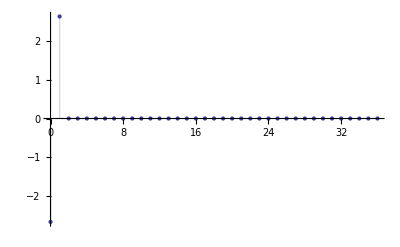

```mathematica
dra[6,-1,1.05]
```

```mathematica
D1[100,-1,1.3]
```

1.